{{0,0,uz},{0,0,0},{-a,bz,bθ}}

```mathematica
DSolve[x'[t]== -a x[t]+ b n t,x[t],t]
```

{{x[t]→(b n (-1+a t))/a^2+ⅇ^(-a t) C[1]}}

```mathematica
Solve[(b n (-1+a t))/a^2+ⅇ^(-a t) x0== x0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(b n+a^2 x0+b n ProductLog[-(a^2 ⅇ^(-1-(a^2 x0)/(b n)) x0)/(b n)])/(a b n)}}

```mathematica
(b n (-1+a /ν0))/a^2+ⅇ^(-a /ν0) x0
```

```mathematica
(b n (-1+a t))/a^2+ⅇ^(-a t) x0/.{t-> 1/n}//FullSimplify
```

(b (a-n))/a^2+ⅇ^(-a/n) x0

```mathematica
Series[1/(1 + 1/(2 s)),{s,0,1}]
```

2 s+O[s]^2

```mathematica
A = {{0,0,uz},{0,0,uy},{bz,0,-a}}
```

{{0,0,uz},{0,0,uy},{bz,0,-a}}

```mathematica
MatrixExp[A t]//Simplify//MatrixForm
```

(2 bz uz ((ⅇ^(1/2 t (-a+√(a^2+4 bz uz))))/(a^2+4 bz uz-a √(a^2+4 bz uz))+(ⅇ^(-1/2 t (a+√(a^2+4 bz uz))))/(a^2+4 bz uz+a √(a^2+4 bz uz))) | 0 | (ⅇ^(-1/2 t (a+√(a^2+4 bz uz))) (-1+ⅇ^(t √(a^2+4 bz uz))) uz)/(√(a^2+4 bz uz))
uy (-1/uz+2 bz ((ⅇ^(1/2 t (-a+√(a^2+4 bz uz))))/(a^2+4 bz uz-a √(a^2+4 bz uz))+(ⅇ^(-1/2 t (a+√(a^2+4 bz uz))))/(a^2+4 bz uz+a √(a^2+4 bz uz)))) | 1 | (ⅇ^(-1/2 t (a+√(a^2+4 bz uz))) (-1+ⅇ^(t √(a^2+4 bz uz))) uy)/(√(a^2+4 bz uz))
(bz ⅇ^(-1/2 t (a+√(a^2+4 bz uz))) (-1+ⅇ^(t √(a^2+4 bz uz))))/(√(a^2+4 bz uz)) | 0 | (ⅇ^(-1/2 t (a+√(a^2+4 bz uz))) (a^2 (1+ⅇ^(t √(a^2+4 bz uz)))+4 bz (1+ⅇ^(t √(a^2+4 bz uz))) uz-a (-1+ⅇ^(t √(a^2+4 bz uz))) √(a^2+4 bz uz)))/(2 (a^2+4 bz uz)))

```mathematica
-(a ⅇ^(1/2 t (bz-√(bz^2-4 a uz))) (-1+ⅇ^(t √(bz^2-4 a uz))))/(√(bz^2-4 a uz))//FullSimplify
```

-(2 a ⅇ^((bz t)/2) Sinh[1/2 t √(bz^2-4 a uz)])/(√(bz^2-4 a uz))

```mathematica
Plot[ (1-2  uz bz ((ⅇ^(1/2 t (-a+√(a^2+4 bz uz))))/(a^2+4 bz uz-a √(a^2+4 bz uz))+(ⅇ^(-1/2 t (a+√(a^2+4 bz uz))))/(a^2+4 bz uz+a √(a^2+4 bz uz))))/.{t-> 1/Log[2],a-> 0.2,uz-> 5},{bz,0,-10},PlotRange-> All]
```

-Graphics-

```mathematica
(1-2  uz bz ((ⅇ^(1/2 t (-a+√(a^2+4 bz uz))))/(a^2+4 bz uz-a √(a^2+4 bz uz))+(ⅇ^(-1/2 t (a+√(a^2+4 bz uz))))/(a^2+4 bz uz+a √(a^2+4 bz uz))))//FullSimplify
```

1+ⅇ^(-(a t)/2) (-Cosh[1/2 t √(a^2+4 bz uz)]-(a Sinh[1/2 t √(a^2+4 bz uz)])/(√(a^2+4 bz uz)))

```mathematica
(1-2  uz bz ((ⅇ^(1/2 t (-a+√(a^2+4 bz uz))))/(a^2+4 bz uz-a √(a^2+4 bz uz))+(ⅇ^(-1/2 t (a+√(a^2+4 bz uz))))/(a^2+4 bz uz+a √(a^2+4 bz uz))))/.{t-> 1/Log[2],a->0.01,bz->-1,uz-> 9}
```

1.37376+0. ⅈ

```mathematica
√(a^2+4 bz uz)/.{t-> 1/Log[2],a->0.01,bz->-1,uz-> 9}
```

0.+5.99999 ⅈ

```mathematica
1+ⅇ^(-(a t)/2) (-Cosh[1/2 t √(a^2+4 bz uz)]-(a Sinh[1/2 t √(a^2+4 bz uz)])/(√(a^2+4 bz uz)))
```

```mathematica
D[(1-2  uz bz ((ⅇ^(1/2 t (-a+√(a^2+4 bz uz))))/(a^2+4 bz uz-a √(a^2+4 bz uz))+(ⅇ^(-1/2 t (a+√(a^2+4 bz uz))))/(a^2+4 bz uz+a √(a^2+4 bz uz)))),uz]
```

```mathematica
Solve[-2 bz ((ⅇ^(1/2 t (-a+√(a^2+4 bz uz))))/(a^2+4 bz uz-a √(a^2+4 bz uz))+(ⅇ^(-1/2 t (a+√(a^2+4 bz uz))))/(a^2+4 bz uz+a √(a^2+4 bz uz)))-2 bz uz (-(ⅇ^(1/2 t (-a+√(a^2+4 bz uz))) (4 bz-(2 a bz)/(√(a^2+4 bz uz))))/((a^2+4 bz uz-a √(a^2+4 bz uz))^2)+(bz ⅇ^(1/2 t (-a+√(a^2+4 bz uz))) t)/(√(a^2+4 bz uz) (a^2+4 bz uz-a √(a^2+4 bz uz)))-(ⅇ^(-1/2 t (a+√(a^2+4 bz uz))) (4 bz+(2 a bz)/(√(a^2+4 bz uz))))/((a^2+4 bz uz+a √(a^2+4 bz uz))^2)-(bz ⅇ^(-1/2 t (a+√(a^2+4 bz uz))) t)/(√(a^2+4 bz uz) (a^2+4 bz uz+a √(a^2+4 bz uz))))==0,bz]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{bz→0}}

```mathematica
B = {{1,-Log[2],0},{0,1,0},{0,0,1}}
M ={ {0,0,uy},{0,0,uθ},{by,bθ,a}};
```

{{1,-Log[2],0},{0,1,0},{0,0,1}}

```mathematica
Inverse[B]//MatrixForm
```

(1 | Log[2] | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
B.M.Inverse[B]//MatrixForm
```

(0 | 0 | uy-uθ Log[2]
0 | 0 | uθ
by | bθ+by Log[2] | a)

```mathematica
B.M.Inverse[B]//MatrixForm
```

(0 | 0 | uy-uθ Log[2]
0 | 0 | uθ
by | bθ+by Log[2] | a)

```mathematica
Inverse[M]
```

Inverse::sing: Matrix {{0,0,uy},{0,0,uθ},{by,bθ,a}} is singular.

Inverse[{{0,0,uy},{0,0,uθ},{by,bθ,a}}]

```mathematica
M = {{0,uz},{-a,bz}}
```

{{0,uz},{-a,bz}}

```mathematica
Inverse[M].{d,0}
```

{(bz d)/(a uz),d/uz}

```mathematica
{{0,1},{-1,0}}//Eigenvalues
```

{ⅈ,-ⅈ}

```mathematica
W = Transpose[{{-1,Exp[-D]},{1,-Exp[-D]}}]
```

{{-1,1},{ⅇ^-D,-ⅇ^-D}}

```mathematica
NullSpace[Transpose[W]]
```

{{ⅇ^-D,1}}

```mathematica
H = {{ⅇ^(-D/2),0},{0,1}}.W.{{1/ⅇ^(-D/2),0},{0,1}}
```

{{-1,ⅇ^(-D/2)},{ⅇ^(-D/2),-ⅇ^-D}}

```mathematica
H/I
```

Hermitian[{{-1,ⅇ^(-D/2)},{ⅇ^(-D/2),-ⅇ^-D}}]

```mathematica
Sum[Exp[-λ j^2],{j,1,∞}]
```

1/2 (-1+EllipticTheta[3,0,ⅇ^-λ])

```mathematica
Sum[Exp[-λ (j+k) - θ(k-j)],{k,1,∞},{j,k,∞}]
```

-ⅇ^λ/((ⅇ^θ-ⅇ^λ) (-1+ⅇ^(2 λ)))

0

```mathematica
Sum[Exp[-λ j-θ j],{j,1,∞}]
```

1/(-1+ⅇ^(θ+λ))

```mathematica
ξ = d/((Exp[λ1]-1)(Exp[θ + λ1]-1))
η = d Exp[λ1]/((Exp[λ1]-1)^2(Exp[θ]-Exp[λ1])(Exp[λ1]-1))
```

d/((-1+ⅇ^λ1) (-1+ⅇ^(θ+λ1)))

(d ⅇ^λ1)/((ⅇ^θ-ⅇ^λ1) (-1+ⅇ^λ1)^3)

ⅇ^(2 x)/((-1+ⅇ^x) (-1+ⅇ^(x+θ)) √(1+(2 ⅇ^(3 x))/((-1+ⅇ^x)^3 (-ⅇ^x+ⅇ^θ))))

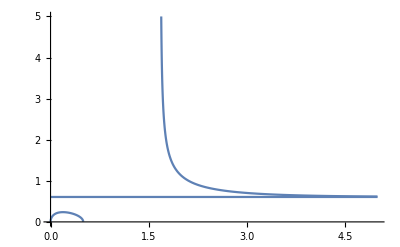

```mathematica
pred = ξ λ2 /Sqrt[1+2 λ2 η]/.{λ1->x,λ2-> Exp[2 x ],d-> 1}
Plot[{Exp[-θ],pred }/.{θ->0.5},{x,0,5},PlotRange-> {0,5}]
```

ⅇ^(2 y)/((-1+ⅇ^x) (-1+ⅇ^(1+x)) √(1+(2 ⅇ^(x+2 y))/((ⅇ-ⅇ^x) (-1+ⅇ^x)^3)))

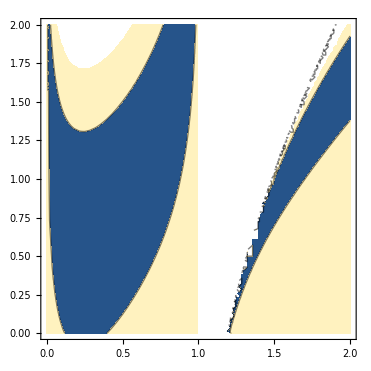

```mathematica
pred = ξ λ2 /Sqrt[1+2 λ2 η]/.{λ1->x,λ2-> Exp[2 y ],d-> 1,θ-> 1}
ContourPlot[(pred - Exp[-1])^2,{x,0,2},{y,0,2},Contours-> {0.05}]
```

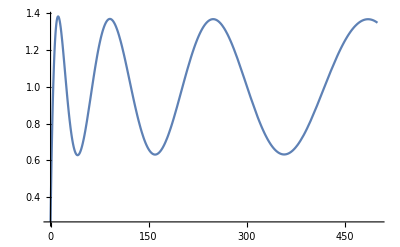

```mathematica
Plot[1 - Exp[-1](Cos[Sqrt[z]]+ 1/Sqrt[z] Sin[Sqrt[z]]),{z,0,500}]
```

```mathematica
D[1 - Exp[-1](Cos[Sqrt[z]]+ 1/Sqrt[z] Sin[Sqrt[z]]),z]
```

```mathematica
Solve[-(Cos[√z]/(2 z)-Sin[√z]/(2 z^(3/2))-Sin[√z]/(2 √z))/ⅇ==0,z]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(Cos[√z]/(2 z)-Sin[√z]/(2 z^(3/2))-Sin[√z]/(2 √z))/ⅇ==0,z]

```mathematica
Sum[2^j,{j,1,n-k}]/Sum[2^j,{j,1,n}]//FullSimplify
```

```mathematica
(2^-k (-2^k+2^n))/2^n//Simplify
```

2^-k-2^-n

```mathematica
2^j/2^n
```

2^(j-n)

```mathematica
(2^(-j+n) (-1+2^j))/(-1+2^n)
```

2^(-1+n)/(-1+2^n)

```mathematica
(2^(-j+n) (-1+2^j))/(-1+2^n)/.{j-> }
```

2^(-1+n)/(-1+2^n)

```mathematica
Sum[2^(n-k),{k,j,n}]/Sum[2^(n-k),{k,1,n}]//Simplify
```

```mathematica
2^(1-j+n)/2^n
```

```mathematica
Sum[2^(1-j),{j,0,n}]
```

2^(1-n) (-1+2^(1+n))

```mathematica
(2^-j (-2^j+2^(1+n)))/(-1+2^n)//FullSimplify
```

```mathematica
alphaSHO[a_,ω0_,ν0_,η_]:=Module[{expTerm,ρTilde,θ,trigTerm},expTerm=Exp[-a/(2 ν0)];
ρTilde=Sqrt[-(1-(η/2)^2)];(*note the minus sign under sqrt*)θ=ω0*ρTilde/ν0;
trigTerm=Cosh[θ]+(a/(2 ω0 ρTilde))*Sinh[θ];
Abs[1-expTerm*trigTerm]]
```

```mathematica
alphaSHO[ω0 * η,ω0 ,1/Log[2]η]
```

```mathematica
Log[2]//N
```

0.693147

```mathematica
Gamma[2,Exp[-y]]
```

Gamma[2,ⅇ^-y]

```mathematica
2*60
```

```mathematica
10*10
```

100

```mathematica
60*2
```

120

```mathematica
2^10
```

1024

```mathematica
2^12
```

4096

```mathematica
2^3
```

8

```mathematica
2^7
```

128

```mathematica
A = {{-1,1},{0,1}}
```

{{1,1}}

```mathematica
uz.
```

2

{{-1,5}}

```mathematica
{{-2,0}}
```

{{-2,0}}

```mathematica
D[1 - Exp[-aa/n](Cos[w/n]+ aa/w Sin[w/n]),w]
```

```mathematica
-ⅇ^(-aa/n) ((aa Cos[w/n])/(n w)-Sin[w/n]/n-(aa Sin[w/n])/w^2)=
```

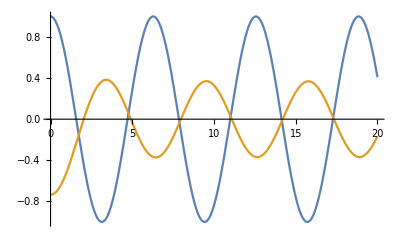

```mathematica
Plot[{Cos[w], - Exp[-1/1](Cos[w/1]+ 1/w Sin[w/1])},{w,0,20}]
```

```mathematica
Cos[I x]
```

Cosh[x]